# D-brane inflation (p=4) Model

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=Λ^4*(1-((m/k)/x)^4)
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1=1. In this case an approximation is required in order to solve the equation. We try to avoid arithmetic solution if it is possible.

```mathematica
Solve[(8 a m^8)/((k^5 x^5)^2)==1,x]
```

{{x→-(2^(3/10) a^(1/10) m^(4/5))/k},{x→(2^(3/10) a^(1/10) m^(4/5))/k},{x→-((-1)^(1/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→((-1)^(1/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→-((-1)^(2/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→((-1)^(2/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→-((-1)^(3/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→((-1)^(3/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→-((-1)^(4/5) 2^(3/10) a^(1/10) m^(4/5))/k},{x→((-1)^(4/5) 2^(3/10) a^(1/10) m^(4/5))/k}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=(2^(3/10) a^(1/10) m^(4/5))/k// Simplify
```

(2^(3/10) a^(1/10) m^(4/5))/k

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[-(k^2/a)*(v[x]/v'[x]),x]
```

(1/2 k^2 m^4 x^2-(k^6 x^6)/6)/(4 a m^4)

```mathematica
Solve[(-(k^6 xf^6)/6)/(4 a m^4)-((-(k^6 x^6)/6)/(4 a m^4))==Y,x]
```

{{x→-(2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k},{x→(2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k},{x→-((-1)^(1/3) 2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k},{x→((-1)^(1/3) 2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k},{x→-((-1)^(2/3) 2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k},{x→((-1)^(2/3) 2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k}}

```mathematica
xi=(2^(1/6) (2^(4/5) a^(3/5) m^(24/5)+12 a m^4 Y)^(1/6))/k// Simplify
```

((2 2^(4/5) a^(3/5) m^(24/5)+24 a m^4 Y)^(1/6))/k

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
ε1i=ε1 /. x->xi// Simplify;
ε2i=ε2 /. x->xi// Simplify;
εi=ε /. x->xi// Simplify;
η1i=η1 /. x->xi// Simplify;
ηi=η/. x->xi// Simplify;
```

For these specific observational indices there is no need for Taylor approximation because no results can be obtained. So, we proceed with the primordial density perturbation and the tensor to scalar ratio:

```mathematica
ns=1-6*ε1i+2*η1i// Simplify;
ns60=ns/. Y->60//Simplify
r=16*ε1i// Simplify;
r60=r/. Y->60// Simplify
```

1-(40 a)/(1440 a+2 2^(4/5) a^(3/5) m^(4/5)-(1440 a m^4+2 2^(4/5) a^(3/5) m^(24/5))^(1/3))-(48 a m^8)/((-m^4 (1440 a m^4+2 2^(4/5) a^(3/5) m^(24/5))^(1/6)+(1440 a m^4+2 2^(4/5) a^(3/5) m^(24/5))^(5/6))^2)

(128 a m^8)/((-m^4 (1440 a m^4+2 2^(4/5) a^(3/5) m^(24/5))^(1/6)+(1440 a m^4+2 2^(4/5) a^(3/5) m^(24/5))^(5/6))^2)

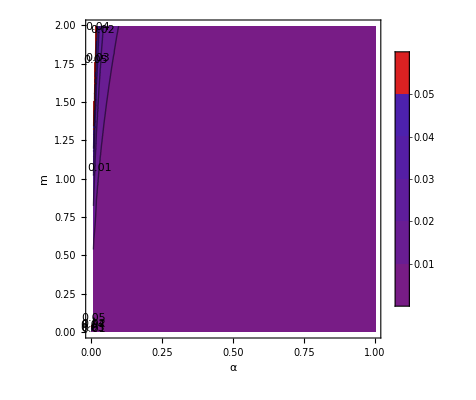

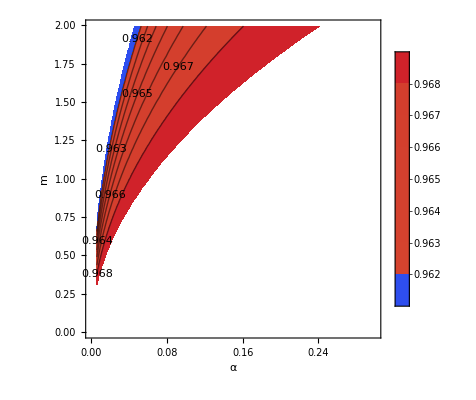

```mathematica
ContourPlot[r60,{a,0,1},{m,10^(-6),1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,0.056}]
ContourPlot[ns60,{a,0,0.3},{m,0.15,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->7,PlotRange->{0.9607,0.9691}]
```

We proceed with the calculation of the contour plots of the slow-roll parameters

```mathematica
ε1i60=ε1i/.Y->60// Simplify;
ε2i60=ε2i/. Y->60// Simplify;
εi60=εi/. Y->60// Simplify;
ηi60=ηi/.Y->60// Simplify;
η1i60=η1i/.Y->60// Simplify;
```

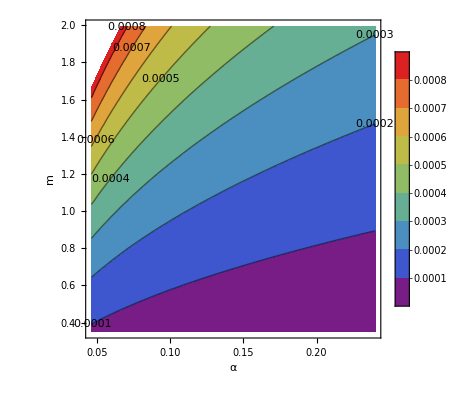

```mathematica
ContourPlot[ε1i60,{a,0.046,0.24},{m,0.35,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

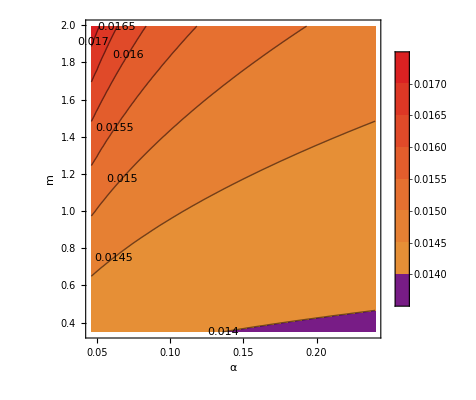

```mathematica
ContourPlot[ε2i60,{a,0.046,0.24},{m,0.35,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

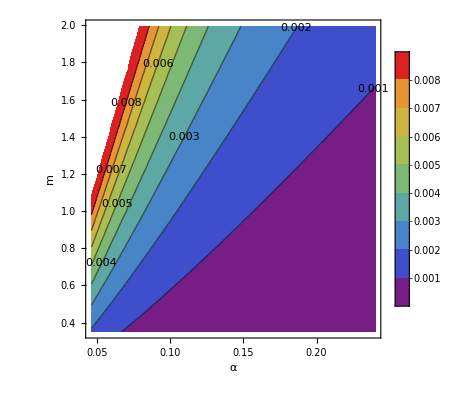

```mathematica
ContourPlot[εi60,{a,0.046,0.24},{m,0.35,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

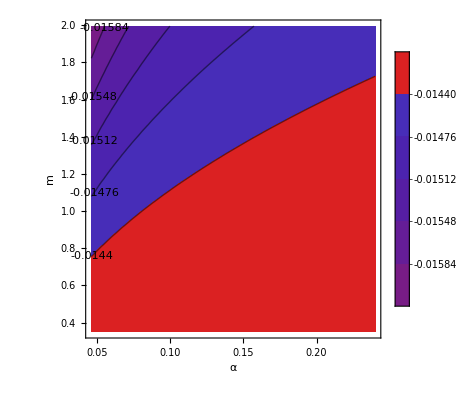

```mathematica
ContourPlot[η1i60,{a,0.046,0.24},{m,0.35,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->5]
```

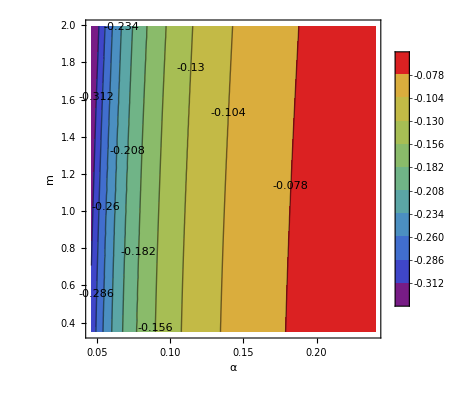

```mathematica
ContourPlot[ηi60,{a,0.046,0.24},{m,0.35,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic,Contours->10]
```

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

```mathematica
s1=v'[x]/v[x]// Simplify;
s1initial=s1/. x->xi// Simplify;
s1initial60=s1initial/. Y->60// Simplify;
s1initial60k=s1initial60/. k->1//Simplify;
```

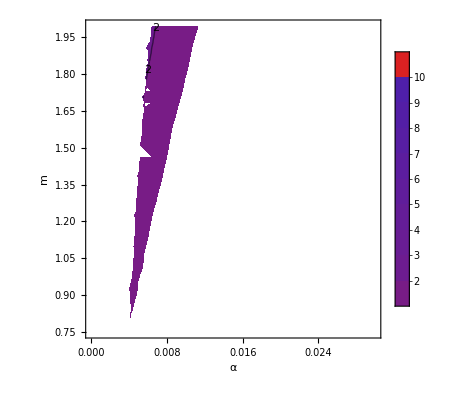

```mathematica
ContourPlot[s1initial60k,{a,0,0.03},{m,0.75,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotRange->{1,10},PlotLegends->Automatic]
```

```mathematica
s2=-v''[x]/v[x]// Simplify;
s2initial=s2/. x->xi// Simplify;
s2initial60=s2initial/. Y->60// Simplify;
s2initial60k=s2initial60/. k->1//Simplify;
```

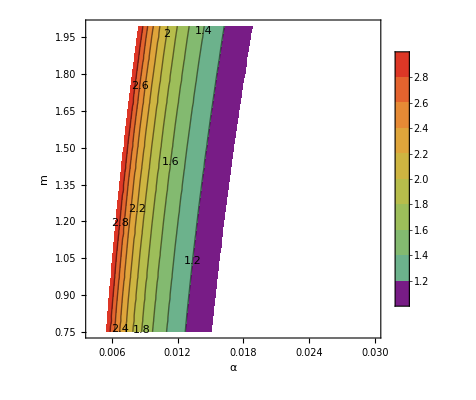

```mathematica
ContourPlot[s2initial60k,{a,0,0.03},{m,0.75,1.99526},FrameLabel->{"α","m"},ContourLabels->True,ColorFunction->"Rainbow",PlotRange->{1,3},PlotLegends->Automatic]
```